```mathematica
(*Chua circuit with a simple limiter where the x dimension limits itself*)
```

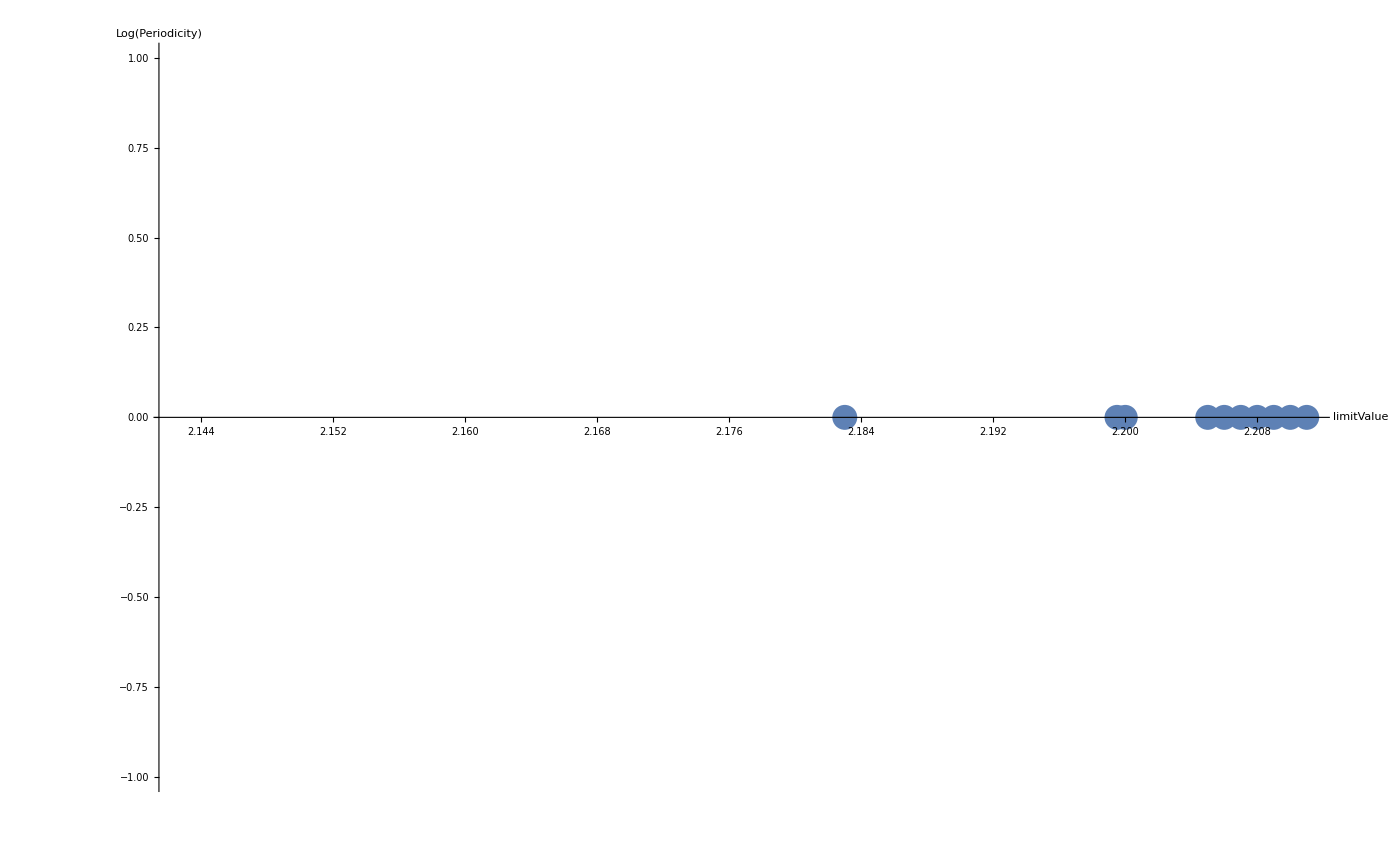

/media/leviathan/SPACE/meta/Work.Repositories/git/minemonics/Minemonics/doc/reports/Thesis/Pictures/controllers/chua-circuit/build/x-limits-z-periodicityParameters013.png

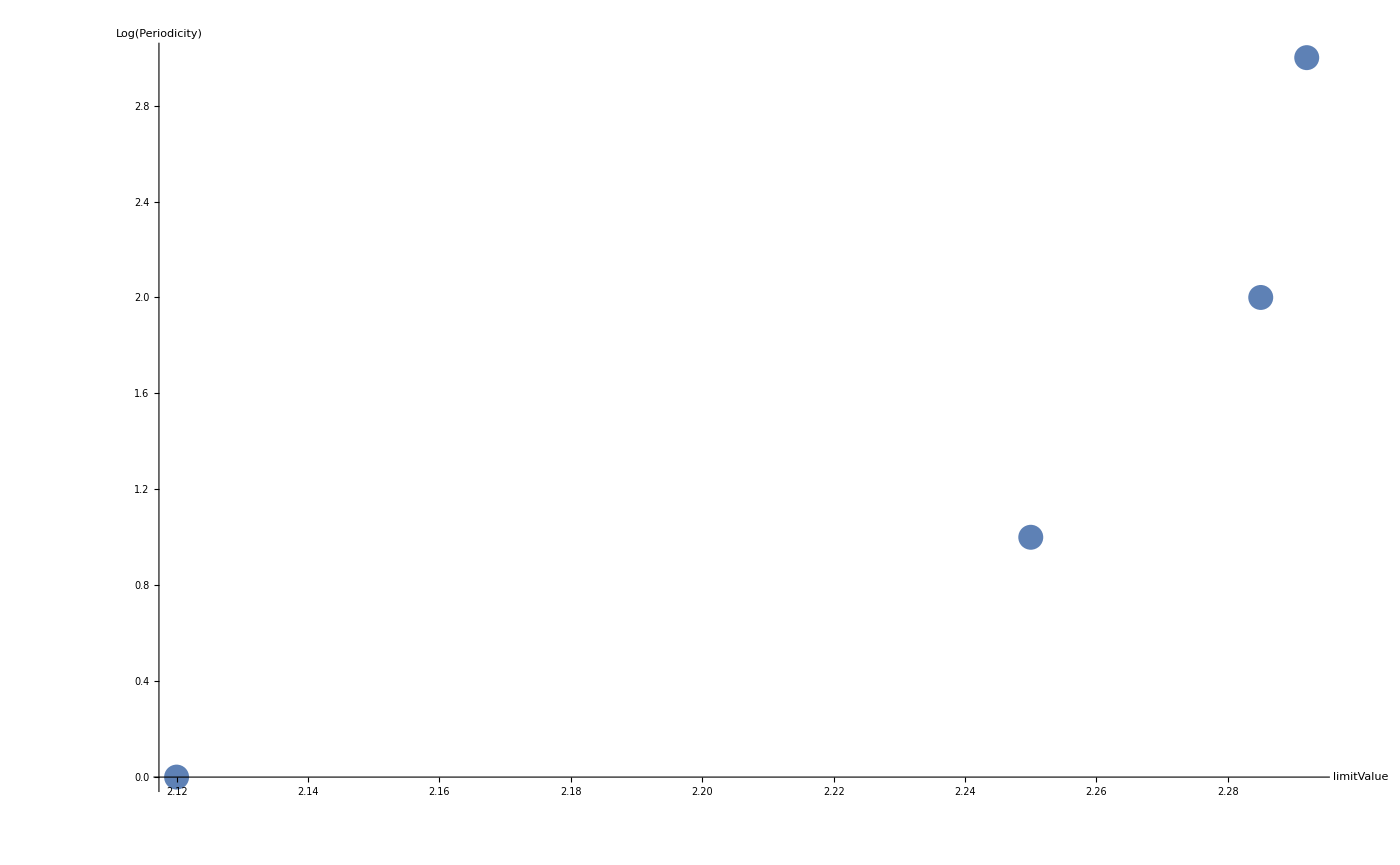

/media/leviathan/SPACE/meta/Work.Repositories/git/minemonics/Minemonics/doc/reports/Thesis/Pictures/controllers/chua-circuit/build/x-limits-z-periodicityParameters05.png

```mathematica
hardLim[x_]:=Piecewise[{{0,x>limitValue},{1,x≤limitValue}}]; (* A hard limiter using a piecewise function *)
softLim[x_]:=(1/2)*(Tanh[ (limitValue-x)/softness]+1); (* A soft limiter using a tanh *)

(*Define the chua circuit's differential equations *)
g[x_] := m0 * x + (m1-m0)/2 * (Abs[x+b]-Abs[x-b]);
f[{x_,y_,z_}]:={c1 * (y-x-g[x]),c2*(x-y+z),-c3*y limiter[x] };

(*RK4 Runge Kutta method based on: 
https://en.wikipedia.org/wiki/Runge%E2%80%93Kutta_methods*)
h = 0.001;
RK4 := Module[{y}, 
k1 = h*f[x];
k2 = h*f[x+k1/2];
k3=h*f[x+k2/2];
k4=h*f[x+k3];
y=x+1/6*(k1+2*k2+2*k3+k4);
x = y;
Return[x]];

RK6 := Module[{y}, 
k1 = h*f[x];
k2 = h*f[x+k1/4];
k3=h*f[x+(3.0/32.0)*k1+(9.0/32.0)*k2];
k4=h*f[x+(1932.0/2197.0)*k1-(7200.0/2197.0)*k2
+(7296.0/2197.0)*k3];
k5 = h *f[x+(439.0/216.0)*k1-8.0*k2+(3680.0/513.0)*k3
-(845.0/4104.0)*k4];
k6 = h * f[x-(8.0/27.0)*k1+2.0*k2-(3544.0/2565.0)*k3
+(1859.0/4104.0)*k4-(11.0/40.0)*k5];
y=x+(16.0/135.0)*k1+(6656.0/12825.0)*k3
+(28561.0/56430.0)*k4-(9.0/50.0)*k5+(2.0/55.0)*k6;
x = y;
Return[x]];

x ={-1.5,0,0};
c1=15.6;
c2 =1;
c3 = 28;
m0=-0.714; (*slope in outer region default:-0.714 *)
m1 = -1.143; (*slope in inner region /default: -1.143 *)
b =1; (*Breakpoints *)

limiter = softLim; (* Choose the softlimiter *)
limitValue =2;
(*For softness 0.13:
1.82 1.83/Period 1 limit cycle (1 to converge) /
2.15/Period 1 limit cycle (high to converge)/
2.183/Period 1 limit cycle (2 to converge)/
2.1995/Period 1 limit cycle (3 to converge)/
2.2/Period 1 limit cycle (4 to converge)/
2.205/Period 1 limit cycle (5 to converge)/
2.206/Period 1 limit cycle (6 to converge)/
2.207/Period 1 limit cycle (7 to converge)/
2.208/Period 1 limit cycle (8 to converge)/
2.209/Period 1 limit cycle (9 to converge)/
2.21/Period 1 limit cycle (10 to converge)/
2.211/Period 1 limit cycle (11 to converge)/

2.215/Period 24 limit cycle/
2.28-2.4 High period limit cycle/Chaos/
2.4-3.19/Chaos/
>3.19/not limited/*)

(* For softness 0.5:
   2.12/ Period 1 limit cycle/
2.25/ Period 2 limit cycle/
2.285/ Period 4 limit cycle/
2.292/ Period 8 limit cycle/
2.2945 /Period 16 limit cycle (?)/
*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

n =40000;

baseImagePath = NotebookDirectory[] <> "build/";

imageSize = 1400; (*Output image width*)
(*0.13*)
periodicityParameters013 = {{1.83,1},{2.183,1},{2.1995,1},{2.2,1},{2.205,1},{2.206,1},{2.207,1},{2.208,1},{2.209,1},{2.21,1},{2.211,1}};
periodicityParameters013[[All,2]] =Log2[periodicityParameters013[[All,2]]];

(*0.5*)
periodicityParameters05 = {{2.12,1},{2.25,2},{2.285,4},{2.292,8}};
periodicityParameters05[[All,2]] =Log2[periodicityParameters05[[All,2]]];

 periodicity013Plot = ListPlot[periodicityParameters013,ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"limitValue","Log(Periodicity)"}]

Export[baseImagePath<>"x-limits-z-periodicityParameters013.png",periodicity013Plot,Background->None]

 perodicity05Plot = ListPlot[periodicityParameters05,ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"limitValue","Log(Periodicity)"}]

Export[baseImagePath<>"x-limits-z-periodicityParameters05.png",perodicity05Plot,Background->None]
```

```mathematica
(*Unlimited-chua-circuit*)
imageName = "Unlimited-chua-circuit";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =50; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3+0.5;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Limit cycle*)
Graphics3D[Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],Graphics3D[Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],
(*Convergence*)
Graphics3D[Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> ".png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-z-softness*)
imageName = "Limited-chua-circuit-z-softness-0-13-3";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =3; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3+0.5;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Limit cycle*)
Graphics3D[Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],Graphics3D[Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],
(*Convergence*)
Graphics3D[Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> ".png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-z-softness*)
imageName = "Limited-chua-circuit-z-softness-0-13-2-8";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.8; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3+0.5;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Limit cycle*)
Graphics3D[Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],Graphics3D[Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],
(*Convergence*)
Graphics3D[Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> ".png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-z-softness*)
imageName = "Limited-chua-circuit-z-softness-0-13-2-6";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.6; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3+0.5;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Limit cycle*)
Graphics3D[Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],Graphics3D[Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],
(*Convergence*)
Graphics3D[Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> ".png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-z-softness*)
imageName = "Limited-chua-circuit-z-softness-0-13-2-4";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.4; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3+0.5;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Limit cycle*)
Graphics3D[Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],Graphics3D[Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],
(*Convergence*)
Graphics3D[Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> ".png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-z-softness*)
imageName = "Limited-chua-circuit-z-softness-0-13-2-375";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.375; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3+0.5;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Limit cycle*)
Graphics3D[Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],Graphics3D[Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],
(*Convergence*)
Graphics3D[Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> ".png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-z-softness*)
imageName = "Limited-chua-circuit-z-softness-0-13-2-35125";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.35125; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3+0.5;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Limit cycle*)
Graphics3D[Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],Graphics3D[Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],
(*Convergence*)
Graphics3D[Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> ".png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-z-softness*)
imageName = "Limited-chua-circuit-z-softness-0-13-2-30375";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.30375; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3+0.5;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Limit cycle*)
Graphics3D[Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],Graphics3D[Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],
(*Convergence*)
Graphics3D[Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> ".png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-z-softness*)
imageName = "Limited-chua-circuit-z-softness-0-13-2-28";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.28; (*Limit of the limiting dimension*)
limitCycleStable = 199999; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3+0.5;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Limit cycle*)
Graphics3D[Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],Graphics3D[Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]],
(*Convergence*)
Graphics3D[Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> ".png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-z-softness*)
imageName = "Limited-chua-circuit-z-softness-0-13-2-183";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.183; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.005],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.005],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-z-softness*)
imageName = "Limited-chua-circuit-z-softness-0-13-2-15";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.15; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.005],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.005],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-z-softness*)
imageName = "Limited-chua-circuit-z-softness-0-13-1-83";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =1.83; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.005],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.005],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-z-softness*)
imageName = "Limited-chua-circuit-z-softness-0-5-2-292";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.292; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-z-softness*)
imageName = "Limited-chua-circuit-z-softness-0-5-2-285";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.285; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-z-softness*)
imageName = "Limited-chua-circuit-z-softness-0-5-2-25";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.25; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```

```mathematica
(*Limited-chua-circuit-z-softness*)
imageName = "Limited-chua-circuit-z-softness-0-5-2-12";
n=200000; (*Number of data points*)
limiter = softLim; (* Choose the softlimiter *)
limitValue =2.12; (*Limit of the limiting dimension*)
limitCycleStable = 20000; (*Number of data points within the stable limit cycle*)
imageSize = 1400; (*Output image width*)
x ={-1.5,0,0}; (*initial conditions*)
softness = 0.5; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

chuaData=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

ymin = Min[chuaData[[All,2]]];
ymax = Max[chuaData[[All,2]]];

(* Plot limits*)
limData = chuaData;
convergenceData = chuaData;

lims = limiter[{chuaData[[All,1]]}];
limData[[All,3]]= Flatten[Transpose[lims]];
convergenceData[[All,3]] = Flatten[Transpose[lims]]*0.3;


(*Export the plot data*)
(*Export[baseImagePath <> imageName <> "-data.dat",chuaPlot];*)

convergencePlot=Show[
(*Convergence*)
Graphics3D[{Thickness[0.001],Opacity[0.1],Point[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
Graphics3D[{Thickness[0.001],Opacity[0.1],Line[chuaData[[1;;n-limitCycleStable,1;;3]],VertexColors->ColorData["PigeonTones"]/@convergenceData[[1;;n-limitCycleStable,3]]]}],
(*Limit cycle*)
Graphics3D[{Thickness[0.001],Point[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],Graphics3D[{Thickness[0.001],Line[chuaData[[n-limitCycleStable;;n,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limData[[n-limitCycleStable;;n,3]]]}],
Graphics3D[{Thick,Red,Line[{{limitValue,ymin,-2.4},{limitValue,ymax,-2.4}}],Text[limitValue,{limitValue+0.2,ymax,-2.4}]}],
Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"x","y","z"},ImageSize->imageSize,BoxRatios->{1,1,1/GoldenRatio},ImagePadding->50];

Export[baseImagePath<>imageName <> "-convergence.png",convergencePlot,Background->None]

signalPlot= ListPlot[chuaData[[All,3]],ImageSize->imageSize,Axes->True,BaseStyle->{FontSize->Scaled[.02]},AxesLabel->{"t"}];

Export[baseImagePath<>imageName <> "-signal.png",signalPlot,Background->None]
```